```mathematica
If[StringTake[$SystemID,3]=="Win",
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\AvoidedQP\\implementation\\"],
SetDirectory["~/Documents/GitHub/AvoidedQP/reimplementation/"]
]
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/reimplementation

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
```

```mathematica
getAssoc[head_,JRange_,tail_]:=(
result={};
Do[(
file=StringJoin[head,"_1.0_",J,"_",tail,".json"];
sData=Import[StringJoin["data/", file],"RawJSON"];
result=Join[result,sData];
),{J,JRange}];
result
)
```

```mathematica
getStruct[ds_]:=(
sizeAvail=Normal[DeleteDuplicates[ds[Take,"size"]]];
interactionAvail=Normal[DeleteDuplicates[ds[Take,"interaction"]]];
couplingAvail=Normal[DeleteDuplicates[ds[Take,"coupling"]]];
hoppingAvail=Normal[DeleteDuplicates[ds[Take,"hopping"]]];
<|"size"->sizeAvail,"interaction"->interactionAvail,"coupling" ->couplingAvail, "hopping"->hoppingAvail|>
)
```

```mathematica
extractData[ds_,directive_,keys_,n_]:=(
data=Apply[ds,directive];
{x,y}=Table[(data[Take,keys[[i]]]//Normal)[[1]],{i,1,2}];
(*AppendTo[x,1000];
AppendTo[y,Table[1000,Length[y[[1]]]]];*)
Table[Table[{Pi x[[i]](*-1/n*),y[[i,s]]},{i,Length[x]}],{s,Length[y[[1]]]}]
)
```

```mathematica
getDPlot[spc_,n_]:=(
SetOptions[LinTicks,TickLengthScale->1.5];

markerFunction[x_]:=If[x,{"●",12},{"○",12}];
markerIndicators=Table[Map[#>10^-20&,(Select[spcDataset,#interaction==B&][Take,"weights"][[1,it]]//Normal)],{it,spcAvail["size"][[1]]+1}];
marks=MapAt[markerFunction,markerIndicators,{All,All}];

plt=ListPlot[Partition[Flatten[spc,1],1],
ImageSize->Medium,
Joined->False,
PlotMarkers->Flatten[Transpose[marks],1],
(*Mesh->15,*)
PlotStyle->Opacity[0.4,If[B==0.,Purple,Orange]],
Frame->True,Axes->False,
FrameStyle->Directive[Black,28,FontFamily->"Bookman Old Style"],
LabelStyle->Directive[Black,24],
(*InterpolationOrder->0,*)
PlotRange->{{0,Pi},{-1.5,0.0}},
PlotRangeClipping->None,
(*PlotLegends->Placed[Automatic,Right],*)
ClippingStyle->Automatic,
AspectRatio->0.75,
FrameLabel->{"p","ω / t"},Epilog->{
Text[
Style[If[B==0,"(f)  λ = 0","(e)  λ = 1"],Black,24,FontFamily->"Bookman Old Style"],
{Pi/5,-0.15}]
},
FrameTicks->{{LinTicks[-2,1,1,10],StripTickLabels[LinTicks[-2,1,1,10]]},{LinTicks[0,Pi,Pi/2,7,TickLabelFunction->(Rationalize[#/Pi]*Pi&)],StripTickLabels[LinTicks[0,Pi,Pi/2,7,TickLabelFunction->(Rationalize[#/Pi]*Pi&)]]}}
];

plt
)
```

```mathematica
makePlotsSpc[]:=(
dirc={Select[#coupling==J&&#size==n&&#interaction==B&]};
keys={"momentum","spectrum"};

plots={};
Do[(
Do[(
buff={};
Do[(
spc=extractData[spcDataset,dirc,keys,n];
AppendTo[buff,getDPlot[spc,n]];
),{B,spcAvail["interaction"]//Normal}];
AppendTo[plots,buff];
),{n,spcAvail["size"]//Normal}];
),{J,spcAvail["coupling"]//Normal}];

plots
)
```

```mathematica
JRange={"0.4"};
tails={"28-2-28_1.0-1.0-1.0"};
head = "dos";
spcPlots={};
Do[(
spcDataset=Dataset[getAssoc[head,JRange,tail]];
spcAvail=Dataset[getStruct[spcDataset]];
AppendTo[spcPlots,makePlotsSpc[]];
),{tail,tails}]
```

```mathematica
spcAvail
```

Dataset[<>]

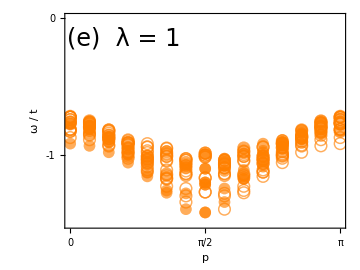

```mathematica
Grid[Reverse[spcPlots[[1]],2]]
```

```mathematica
SavePlots[]:=(
Do[(
Do[(
Do[(
fileName=StringJoin["plots/",head,"/",
head,"_L=",ToString[spcAvail["size"][[iN]]],
"_J=",ToString[spcAvail["coupling"][[iJ]]],
"_B=",ToString[spcAvail["interaction"][[iB]]],
".jpg"];
Export[fileName,spcPlots[[iN,iJ,iB]],ImageResolution->300];
),{iB,Length[spcAvail["interaction"]//Normal]}]
),{iJ,Length[spcAvail["coupling"]//Normal]}]
),{iN,Length[spcAvail["size"]//Normal]}]
)
```

```mathematica
SavePlots[]
```